In this notebook we will be calculating the dimensionless funcitons R_≫ and R_≪

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Global Parameters

```mathematica
nA=9.51514 10^22(* cm *);
Qweff=12.280072222784852;
sw=√0.24;
Uref=10^-1;
VnAref=10^31;
mNref=3(* MeV*);
```

## Solar Neutrinos

```mathematica
pp=({#⟦1⟧,6.03 10^10#⟦2⟧}&)/@Import["SolarNuFlux/pp.dat"];
n13=({#⟦1⟧,2.17 10^8#⟦2⟧}&)/@Import["SolarNuFlux/n13.dat"];
o15=({#⟦1⟧,1.56 10^8#⟦2⟧}&)/@Import["SolarNuFlux/o15.dat"];
f17=({#⟦1⟧,3.4 10^6#⟦2⟧}&)/@Import["SolarNuFlux/f17.dat"];
b8=({#⟦1⟧,4.59 10^6#⟦2⟧}&)/@Import["SolarNuFlux/b8.dat"];
hep=({#⟦1⟧,8.31 10^3#⟦2⟧}&)/@Import["SolarNuFlux/hep.dat"];
be7gs=({10^-3#⟦1⟧+0.8613,4.56 10^9#⟦2⟧}&)/@Import["SolarNuFlux/7be-gs.dat"];
be7ex=({10^-3#⟦1⟧+0.3843,4 10^8#⟦2⟧}&)/@Import["SolarNuFlux/7be-ex.dat"];
MyDelta[x_,σ_]:= 1/(√(2π σ^2))Exp[-1/2 x^2/σ^2];
CutOff[x_,y_]:=UnitStep[y-x];interp=(  Interpolation[#,InterpolationOrder->1][Eν]CutOff[Eν,Last[#]⟦1⟧] &);
ppx =interp @ pp;
n13x =interp @ n13;
o15x= interp @ o15;
f17x=interp @ f17;
b8x=interp@ b8;
hepx=interp @ hep;
be7gsx=4.56 10^9 MyDelta[Eν-0.8613,0.01];
be7exx=4 10^8 MyDelta[Eν-0.3843,0.01];
pepx=1.5 10^8 MyDelta[Eν-1.44,0.01];
SolarNuOfx=ppx+n13x+o15x+f17x+b8x+hepx+be7gsx+pepx;
Pe=<||>;
Pe["e"]=Interpolation[({10^-6#⟦1⟧,#⟦2⟧}&)/@Import["SurvivalProbabilities/Pee.dat"]][Eν];
Pe["μ"]=Interpolation[({10^-6#⟦1⟧,#⟦2⟧}&)/@Import["SurvivalProbabilities/Pem.dat"]][Eν];
Pe["τ"]=Interpolation[({10^-6#⟦1⟧,#⟦2⟧}&)/@Import["SurvivalProbabilities/Pet.dat"]][Eν];
flavours={"e","μ","τ"};
SolarNu=<||>;
Do[SolarNu[flav]=Pe[flav] SolarNuOfx ,{flav,flavours}];
```

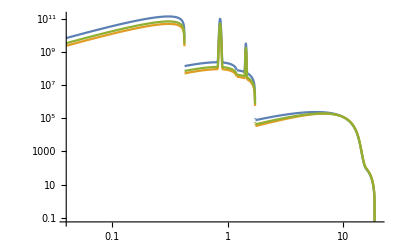

```mathematica
LogLogPlot[{SolarNu["e"],SolarNu["μ"],SolarNu["τ"]},{Eν,0.04,20}]//Quiet
```

## Integrated yield

```mathematica
(*  We are starting from Eq (22) of the article post erratumd  *) 
integrand=<||>;
Do[integrand[flav]=1/10^8 SolarNu[flav] Eν/10,{flav,flavours}];
L[x_]:= Log[(1-3 x^2-(1-x^2)√(1-4 x^2))/(x^2(1+√(1-4 x^2)))];
prefactorSubs[flav_]:= If[flav=="e",{C1->1/4(1-4 sw^2+8 sw^4) ,C2->1/2 sw^2(2 sw^2-1) },{C1->1/4(1+4 sw^2+8 sw^4) ,C2->1/2 sw^2(2 sw^2+1)}]
prefactor=(C1((1-14 x^2-2 x^4-12 x^6)√(1-4 x^2)+ 12 x^4(x^4-1)L[x]) + 4C2(x^2(2+10 x^2-12 x^4)√(1-4 x^2)+6 x^4(1-2 x^2+2 x^4)L[x]))/.x-> 0.511/mN;
yieldCurves=<||>;
Do[yieldCurves[flav]=Interpolation@Table[{mN,(prefactor/.prefactorSubs[flav]) NIntegrate[integrand[flav],{Eν,mN,18.8},Method->{Automatic,"SymbolicProcessing"-> False},AccuracyGoal->5]},{mN,1.1,18.8,0.1}],{flav,flavours}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Eν near {Eν} = {1.45576327598969}. NIntegrate obtained 0.0985098 and 0.000226346 for the integral and error estimates.

## Limit Curves

#### Borexino

```mathematica
numSecInDay=60 60 24;
densityLiqSint=876 (* kg/m3*)*  0.001 (* tonne/kg*) /10^6 (* cm^3/m^3*)//N ;(* from http://borex.lngs.infn.it/Thesis/M.Leung_PhD_Thesis.pdf*) 
fidVolBXNO=100 (*tonne*) / densityLiqSint;
exclEventsBXNO=15;
numDays=446; 
Total@{3,9,5,2,4,4,3,4,5,3,2,1,4,3,3,2,0,1,2,0,1,2,3,3,1,2,0,0,0,0,0,2,1,0,0}; (* Data from *)
```

```mathematica
Do[UexclBXNOCons[flav]=Uref( exclEventsBXNO/((0.06 )*numDays/365.25)  (10^31/(nA fidVolBXNO))(12/Qweff)^2(mNref/mN)^6(1/(yieldCurves[flav][mN]+10^-32)))^(1/4)HeavisideTheta[yieldCurves[flav][mN]+0.000001],{flav,flavours}];
Do[UexclBXNOReal[flav]=Uref((1/5 exclEventsBXNO)/((0.06 )*numDays/365.25)  (10^31/(nA fidVolBXNO))(12/Qweff)^2(mNref/mN)^6(1/(yieldCurves[flav][mN]+10^-32)))^(1/4)HeavisideTheta[yieldCurves[flav][mN]+0.000001],{flav,flavours}];
```

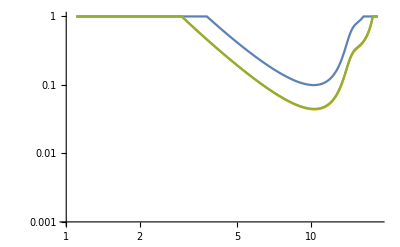

```mathematica
LogLogPlot[{Min[1,UexclBXNOReal["e"]^2],Min[1,UexclBXNOReal["μ"]^2],Min[1,UexclBXNOReal["τ"]^2]},{mN,1.1,18.8},PlotRange->{0.001,1}]
```

#### SK

```mathematica
numSecInDay=60 60 24;
densityH20=1 (* g/cm3*)*  0.001 (* tonne/kg*) 0.001 (* kg/g*)//N ;(* from http://borex.lngs.infn.it/Thesis/M.Leung_PhD_Thesis.pdf*) 
fidVolSK=22.5 10^3 (*tonne*) / densityH20;
rateBoundSK=4.62 (* events per kt day*)*22.5 (*kton*);
UexclSK=<||>;
Do[UexclSK[flav]=Uref( rateBoundSK/((0.22 10^-6 ) numSecInDay)  (VnAref/(nA fidVolSK))(12/Qweff)^2(mNref/mN)^6(1/(yieldCurves[flav][mN]+10^-32)))^(1/4)HeavisideTheta[yieldCurves[flav][mN]+0.000001],{flav,flavours}];
```

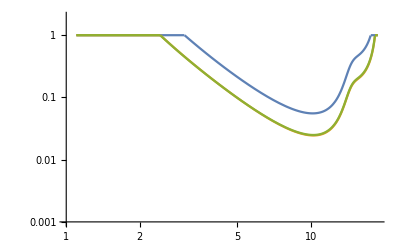

```mathematica
LogLogPlot[{Min[1,UexclSK["e"]^2],Min[1,UexclSK["μ"]^2],Min[1,UexclSK["τ"]^2]},{mN,1.1,18.8},PlotRange->{0.001,2}]
```

```mathematica
fidVolBXNO/fidVolSK
```

4.44444×10^-11 fidVolBXNO

## Plots

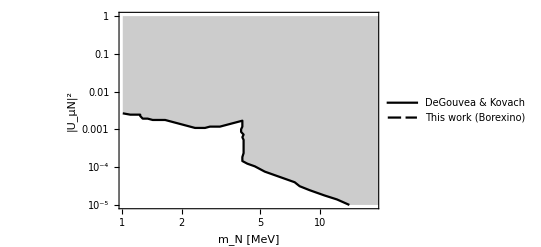

```mathematica
flav="e";
bxno=Table[{mN,UexclBXNO[flav]^2},{mN,0.511 2,18.8,0.01}]//Quiet;
ListLogLogPlot[{Import["ExistingConstraints/e-constraints.csv"],bxno},Joined->True,PlotRange->{{2 0.511,18.8},{10^-5,1}},PlotTheme->"Monochrome",Filling->{Top},PlotMarkers->None,Frame->  True,PlotRangePadding-> 0,PlotLegends->Placed[{"DeGouvea & Kovach", "This work (Borexino)"},{0.3,0.3}],FrameStyle->Black,FrameLabel->(Style[#,13]&)/@{"m_N    [MeV]","|U_μN|^2"}]
Clear[flav]
```

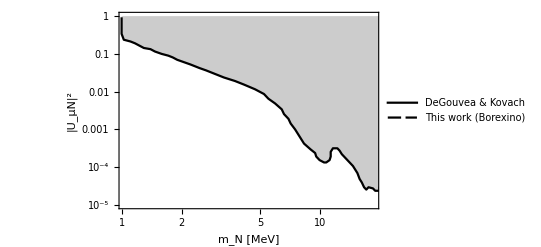

```mathematica
flav="μ";
bxno=Table[{mN,UexclBXNO[flav]^2},{mN,0.511 2,18.8,0.01}]//Quiet;
ListLogLogPlot[{Import["ExistingConstraints/mu-constraints.csv"],bxno},Joined->True,PlotRange->{{2 0.511,18.8},{10^-5,1}},PlotTheme->"Monochrome",Filling->{Top},PlotMarkers->None,Frame->  True,PlotRangePadding-> 0,PlotLegends->Placed[{"DeGouvea & Kovach", "This work (Borexino)"},{0.3,0.3}],FrameStyle->Black,FrameLabel->(Style[#,13]&)/@{"m_N    [MeV]","|U_μN|^2"}]
Clear[flav]
```

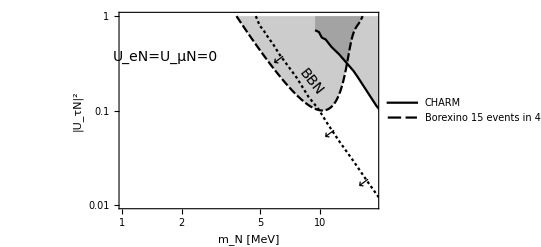

```mathematica
flav="τ";
bxnoCons=Table[{mN,UexclBXNOCons[flav]^2},{mN,0.511 2,18.8,0.01}]//Quiet;
bxnoReal=Table[{mN,UexclBXNOReal[flav]^2},{mN,0.511 2,18.8,0.01}]//Quiet;
ListLogLogPlot[{Import["ExistingConstraints/tau-constraints.csv"],bxnoCons,SortBy[First]@Import["ExistingConstraints/BBN-Bounds-tau.csv"]},Joined->True,PlotRange->{{2 0.511,18.8},{10^-2,1}},PlotTheme->"Monochrome",Filling->{{1-> Top},{2-> Top}},PlotMarkers->None,Frame->  True,PlotRangePadding-> 0,PlotLegends->Placed[{"CHARM", "Borexino 15  events in 446 days"},{0.4,0.25}],FrameStyle->Black,FrameLabel->(Style[#,13]&)/@{"m_N    [MeV]","|U_τN|^2"},Epilog->{Inset[Style["U_eN=U_μN=0",14],{0.5,-1}],Inset[Rotate[Style["BBN",14],-0.9],{2.2,-1.6}],Inset[Rotate[Style["→",15],-2.5],{1.8,-1}],Inset[Rotate[Style["→",15],-2.5],{2.8,-4}],Inset[Rotate[Style["→",15],-2.5],{2.4,-2.8}]}]
Clear[flav]
```